# Método de los momentos - Normal estándar

```mathematica
(*Muestra de la distribución Normal(0,1)*)
```

```mathematica
SeedRandom[1234]
```

```mathematica
data1 = RandomVariate[NormalDistribution[0,1],10001]
```

{-0.508336,-0.0706019,-1.5939,1.53659,2.67802,-1.31683,-1.09456,0.142948,0.104166,-1.67311,0.0357514,0.170186,0.934682,-0.826864,9973,0.622688,-0.538344,1.10496,-0.342243,1.0691,-0.852105,0.249137,1.09009,0.0543596,-1.12438,-1.15048,0.35102,0.954185,-0.387142}
 |  |  |  |

```mathematica
Position[data1,4.160359637556179]
```

{{7615}}

```mathematica
data=Delete[data1,7615]
```

{-0.508336,-0.0706019,-1.5939,1.53659,2.67802,-1.31683,-1.09456,0.142948,0.104166,-1.67311,0.0357514,0.170186,0.934682,-0.826864,9972,0.622688,-0.538344,1.10496,-0.342243,1.0691,-0.852105,0.249137,1.09009,0.0543596,-1.12438,-1.15048,0.35102,0.954185,-0.387142}
 |  |  |  |

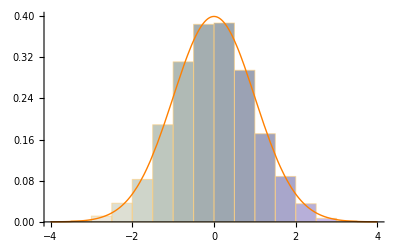

```mathematica
Show[Histogram[data,20,"ProbabilityDensity",ChartStyle->{"PearlColors"}],Plot[PDF[NormalDistribution[0,1],x],{x,-4,4},PlotStyle->{{Orange,Thick}}]]
```

### MOP DE GRADO 3

```mathematica
(*Momentos poblacionales*)
```

```mathematica
Integrate[x*(a+b*x+c*x^2+d*x^3),{x,-4,4}]
```

(128 b)/3+(2048 d)/5

```mathematica
Integrate[x^2*(a+b*x+c*x^2+d*x^3),{x,-4,4}]
```

(128 a)/3+(2048 c)/5

```mathematica
Integrate[x^3*(a+b*x+c*x^2+d*x^3),{x,-4,4}]
```

(2048 b)/5+(32768 d)/7

```mathematica
Integrate[x^4*(a+b*x+c*x^2+d*x^3),{x,-4,4}]
```

(2048 a)/5+(32768 c)/7

```mathematica
(*Solución del sistema*)
```

```mathematica
Solve[{(128 b)/3+(2048 d)/5==(Apply[Plus,data])/(10^4),(128 a)/3+(2048 c)/5==(Apply[Plus,data^2])/(10^4),(2048 b)/5+(32768 d)/7==(Apply[Plus,data^3])/(10^4),(2048 a)/5+(32768 c)/7==(Apply[Plus,data^4])/(10^4)},{a,b,c,d}]
```

{{a→0.107228,b→-0.00215438,c→-0.00874683,d→0.00017641}}

```mathematica
(*Obtención de la función de densidad y representación gráfica*)
```

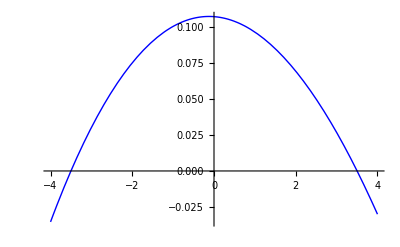

```mathematica
Plot[a+b*x+c*x^2+d*x^3/.{a->0.10722822140852821,b->-0.0021543789364477806,c->-0.008746833003781507,d->0.0001764098791879829},{x,-4,4},PlotStyle->{Blue,Thin}]
```

```mathematica
f[x_]=a+b*x+c*x^2+d*x^3/.{a->0.10722822140852821,b->-0.0021543789364477806,c->-0.008746833003781507,d->0.0001764098791879829}
```

0.107228-0.00215438 x-0.00874683 x^2+0.00017641 x^3

```mathematica
f[-4]
```

-0.0353938

```mathematica
f[4]
```

-0.0300484

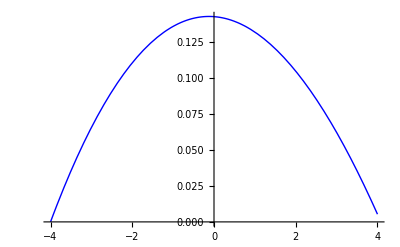

```mathematica
Plot[a+b*x+c*x^2+d*x^3+0.03539382317421569/.{a->0.10722822140852821,b->-0.0021543789364477806,c->-0.008746833003781507,d->0.0001764098791879829},{x,-4,4},PlotStyle->{Blue,Thin}]
```

```mathematica
Integrate[a+b*x+c*x^2+d*x^3+0.03539382317421569/.{a->0.10722822140852821,b->-0.0021543789364477806,c->-0.008746833003781507,d->0.0001764098791879829},{x,-4,4}]
```

0.767778

```mathematica
f3[x_]=(a+b*x+c*x^2+d*x^3+0.03539382317421569)/0.767778148500607/.{a->0.10722822140852821,b->-0.0021543789364477806,c->-0.008746833003781507,d->0.0001764098791879829}
```

1.30246 (0.142622-0.00215438 x-0.00874683 x^2+0.00017641 x^3)

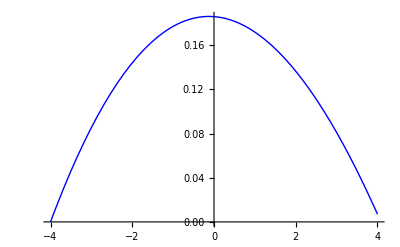

```mathematica
Plot[f3[x],{x,-4,4},PlotStyle->{Blue,Thin}]
```

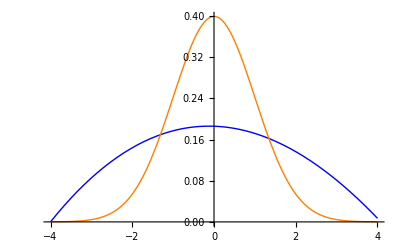

```mathematica
Plot[{f3[x],PDF[NormalDistribution[0,1],x]},{x,-4,4},PlotStyle->{{Blue,Thin},{Orange,Thin}}]
```

```mathematica
(*Divergencia de Kullback-Leibler*)
```

```mathematica
N[Integrate[PDF[NormalDistribution[0,1],x],{x,-4,4}]]
```

0.999937

```mathematica
F[x_]=(PDF[NormalDistribution[0,1],x])/0.9999366575163338
```

0.398968 ⅇ^(-x^2/2)

```mathematica
KL3 = N[Integrate[F[x]*Log[F[x]/f3[x]],{x,-4,4}]]
```

0.333753

```mathematica
(*Verosimilitud*)
```

```mathematica
x3=Log[f3[data]]
```

{-1.69167,-1.68254,-1.83034,-1.86187,-2.29309,-1.77682,-1.74365,-1.68672,-1.68554,-1.84841,-1.68392,-1.68765,-1.75232,-1.71391,9972,-1.71674,-1.69319,-1.7775,-1.68537,-1.77184,-1.71626,-1.69088,-1.77513,-1.68431,-1.74764,-1.75124,-1.69619,-1.75499,-1.68672}
 |  |  |  |

```mathematica
V3 =Apply[Plus,x3]
```

-17514.8

```mathematica
(*BIC*)
```

```mathematica
BIC3 = -2*V3 + 4*Log[10000]
```

35066.4

### MOP DE GRADO 4

```mathematica
(*Momentos poblacionales*)
```

```mathematica
Integrate[x*(a+b*x+c*x^2+d*x^3+e*x^4),{x,-4,4}]
```

(128 b)/3+(2048 d)/5

```mathematica
Integrate[x^2*(a+b*x+c*x^2+d*x^3+e*x^4),{x,-4,4}]
```

(128 a)/3+(2048 c)/5+(32768 e)/7

```mathematica
Integrate[x^3*(a+b*x+c*x^2+d*x^3+e*x^4),{x,-4,4}]
```

(2048 b)/5+(32768 d)/7

```mathematica
Integrate[x^4*(a+b*x+c*x^2+d*x^3+e*x^4),{x,-4,4}]
```

(2048 a)/5+(32768 c)/7+(524288 e)/9

```mathematica
Integrate[x^5*(a+b*x+c*x^2+d*x^3+e*x^4),{x,-4,4}]
```

(32768 b)/7+(524288 d)/9

```mathematica
(*Solución del sistema*)
```

```mathematica
Solve[{(128 b)/3+(2048 d)/5==(Apply[Plus,data])/(10^4),(128 a)/3+(2048 c)/5+(32768 e)/7==(Apply[Plus,data^2])/(10^4),(2048 b)/5+(32768 d)/7==(Apply[Plus,data^3])/(10^4),(2048 a)/5+(32768 c)/7+(524288 e)/9==(Apply[Plus,data^4])/(10^4),(32768 b)/7+(524288 d)/9==(Apply[Plus,data^5])/(10^4)},{a,b,c,d,e}]
```

{}

```mathematica
M={{0,128/3,0,2048/5,0},{128/3,0,2048/5,0,32768/7},{0,2048/5,0,32768/7,0},{2048/5,0,32768/7,0,524288/9},{0,32768/7,0,524288/9,0}}
```

{{0,128/3,0,2048/5,0},{128/3,0,2048/5,0,32768/7},{0,2048/5,0,32768/7,0},{2048/5,0,32768/7,0,524288/9},{0,32768/7,0,524288/9,0}}

```mathematica
MatrixForm[M]
```

(0 | 128/3 | 0 | 2048/5 | 0
128/3 | 0 | 2048/5 | 0 | 32768/7
0 | 2048/5 | 0 | 32768/7 | 0
2048/5 | 0 | 32768/7 | 0 | 524288/9
0 | 32768/7 | 0 | 524288/9 | 0)

```mathematica
Det[M]
```

0

```mathematica
MatrixRank[M]
```

4

```mathematica
MAmpliada = {{0,128/3,0,2048/5,0,(Apply[Plus,data])/(10^4)},{128/3,0,2048/5,0,32768/7,(Apply[Plus,data^2])/(10^4)},{0,2048/5,0,32768/7,0,(Apply[Plus,data^3])/(10^4)},{2048/5,0,32768/7,0,524288/9,(Apply[Plus,data^4])/(10^4)},{0,32768/7,0,524288/9,0,(Apply[Plus,data^5])/(10^4)}}
```

{{0,128/3,0,2048/5,0,-0.0192079},{128/3,0,2048/5,0,32768/7,0.994084},{0,2048/5,0,32768/7,0,-0.049427},{2048/5,0,32768/7,0,524288/9,3.00546},{0,32768/7,0,524288/9,0,-0.231287}}

```mathematica
MatrixForm[MAmpliada]
```

(0 | 128/3 | 0 | 2048/5 | 0 | -0.0192079
128/3 | 0 | 2048/5 | 0 | 32768/7 | 0.994084
0 | 2048/5 | 0 | 32768/7 | 0 | -0.049427
2048/5 | 0 | 32768/7 | 0 | 524288/9 | 3.00546
0 | 32768/7 | 0 | 524288/9 | 0 | -0.231287)

```mathematica
MatrixRank[MAmpliada]
```

5

### MOP DE GRADO 5

```mathematica
(*Momentos poblacionales*)
```

```mathematica
Integrate[x*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5),{x,-4,4}]
```

(128 b)/3+(2048 d)/5+(32768 f)/7

```mathematica
Integrate[x^2*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5),{x,-4,4}]
```

(128 a)/3+(2048 c)/5+(32768 e)/7

```mathematica
Integrate[x^3*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5),{x,-4,4}]
```

(2048 b)/5+(32768 d)/7+(524288 f)/9

```mathematica
Integrate[x^4*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5),{x,-4,4}]
```

(2048 a)/5+(32768 c)/7+(524288 e)/9

```mathematica
Integrate[x^5*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5),{x,-4,4}]
```

(32768 b)/7+(524288 d)/9+(8388608 f)/11

```mathematica
Integrate[x^6*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5),{x,-4,4}]
```

(32768 a)/7+(524288 c)/9+(8388608 e)/11

```mathematica
(*Solución del sistema*)
```

```mathematica
Solve[{(128 b)/3+(2048 d)/5+(32768 f)/7==(Apply[Plus,data])/(10^4),(128 a)/3+(2048 c)/5+(32768 e)/7==(Apply[Plus,data^2])/(10^4),(2048 b)/5+(32768 d)/7+(524288 f)/9==(Apply[Plus,data^3])/(10^4),(2048 a)/5+(32768 c)/7+(524288 e)/9==(Apply[Plus,data^4])/(10^4),(32768 b)/7+(524288 d)/9+(8388608 f)/11==(Apply[Plus,data^5])/(10^4),(32768 a)/7+(524288 c)/9+(8388608 e)/11==(Apply[Plus,data^6])/(10^4)},{a,b,c,d,e,f}]
```

{{a→0.21809,b→-0.00486864,c→-0.0410816,d→0.000968069,e→0.00181883,f→-0.0000445308}}

```mathematica
(*Obtención de la función de densidad y representación gráfica*)
```

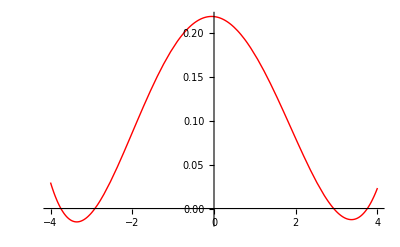

```mathematica
Plot[a+b*x+c*x^2+d*x^3+e*x^4+f*x^5/.{a->0.21809013439759367,b->-0.0048686371543091075,c->-0.041081557625592235,d->0.0009680685260642024,e->0.0018188282599768525,f->-0.000044530798886787326},{x,-4,4},PlotStyle->{Red,Thin}]
```

```mathematica
f[x_]=a+b*x+c*x^2+d*x^3+e*x^4+f*x^5/.{a->0.21809013439759367,b->-0.0048686371543091075,c->-0.041081557625592235,d->0.0009680685260642024,e->0.0018188282599768525,f->-0.000044530798886787326}
```

0.21809-0.00486864 x-0.0410816 x^2+0.000968069 x^3+0.00181883 x^4-0.0000445308 x^5

```mathematica
FindMinimum[f[x],{x,-2.5}]
```

{-0.0151786,{x→-3.35794}}

```mathematica
FindMinimum[f[x],{x,2.5}]
```

{-0.0125935,{x→3.36368}}

```mathematica
Integrate[a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+0.015178620565664078/.{a->0.21809013439759367,b->-0.0048686371543091075,c->-0.041081557625592235,d->0.0009680685260642024,e->0.0018188282599768525,f->-0.000044530798886787326},{x,-4,4}]
```

0.858329

```mathematica
f5[x_]=(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+0.015178620565664078)/0.8583289696339789/.{a->0.21809013439759367,b->-0.0048686371543091075,c->-0.041081557625592235,d->0.0009680685260642024,e->0.0018188282599768525,f->-0.000044530798886787326}
```

1.16505 (0.233269-0.00486864 x-0.0410816 x^2+0.000968069 x^3+0.00181883 x^4-0.0000445308 x^5)

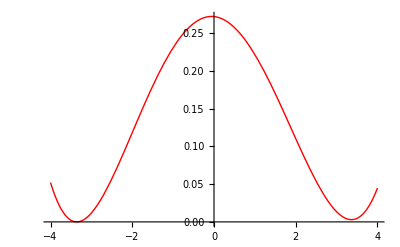

```mathematica
Plot[f5[x],{x,-4,4},PlotStyle->{Red,Thin}]
```

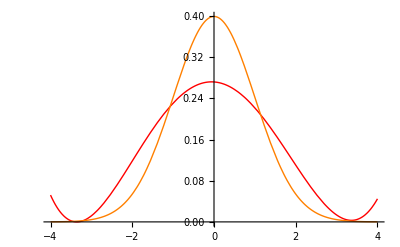

```mathematica
Plot[{f5[x],PDF[NormalDistribution[0,1],x]},{x,-4,4},PlotStyle->{{Red,Thin},{Orange,Thin}}]
```

```mathematica
(*Divergencia de Kullback-Leibler*)
```

```mathematica
KL5= N[Integrate[F[x]*Log[F[x]/f5[x]],{x,-4,4}]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-3.34387}. NIntegrate obtained 0.0953824 and 4.09486×10^-6 for the integral and error estimates.

0.0953824

```mathematica
x5 = Log[f5[data]]
```

{-1.33834,-1.3022,-1.77868,-1.79874,-3.30145,-1.6082,-1.50381,-1.30938,-1.30688,-1.83707,-1.30377,-1.31146,-1.48212,-1.41014,9972,-1.38523,-1.3434,-1.55277,-1.31643,-1.53677,-1.4176,-1.31896,-1.54606,-1.30445,-1.51633,-1.52765,-1.33195,-1.48954,-1.32135}
 |  |  |  |

```mathematica
V5 = Apply[Plus,x5]
```

-15121.7

```mathematica
(*BIC*)
```

```mathematica
BIC5 = -2*V5 + 6*Log[10000]
```

30298.7

### MOP DE GRADO 7

```mathematica
(*Momentos poblacionales*)
```

```mathematica
Integrate[x*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7),{x,-4,4}]
```

(128 b)/3+(2048 d)/5+(32768 f)/7+(524288 h)/9

```mathematica
Integrate[x^2*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7),{x,-4,4}]
```

(128 a)/3+(2048 c)/5+(32768 e)/7+(524288 g)/9

```mathematica
Integrate[x^3*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7),{x,-4,4}]
```

(2048 b)/5+(32768 d)/7+(524288 f)/9+(8388608 h)/11

```mathematica
Integrate[x^4*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7),{x,-4,4}]
```

(2048 a)/5+(32768 c)/7+(524288 e)/9+(8388608 g)/11

```mathematica
Integrate[x^5*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7),{x,-4,4}]
```

(32768 b)/7+(524288 d)/9+(8388608 f)/11+(134217728 h)/13

```mathematica
Integrate[x^6*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7),{x,-4,4}]
```

(32768 a)/7+(524288 c)/9+(8388608 e)/11+(134217728 g)/13

```mathematica
Integrate[x^7*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7),{x,-4,4}]
```

(524288 b)/9+(8388608 d)/11+(134217728 f)/13+(2147483648 h)/15

```mathematica
Integrate[x^8*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7),{x,-4,4}]
```

(524288 a)/9+(8388608 c)/11+(134217728 e)/13+(2147483648 g)/15

```mathematica
(*Solución del sistema*)
```

```mathematica
Solve[{(128 b)/3+(2048 d)/5+(32768 f)/7+(524288 h)/9==(Apply[Plus,data])/(10^4),(128 a)/3+(2048 c)/5+(32768 e)/7+(524288 g)/9==(Apply[Plus,data^2])/(10^4),(2048 b)/5+(32768 d)/7+(524288 f)/9+(8388608 h)/11==(Apply[Plus,data^3])/(10^4),(2048 a)/5+(32768 c)/7+(524288 e)/9+(8388608 g)/11==(Apply[Plus,data^4])/(10^4),(32768 b)/7+(524288 d)/9+(8388608 f)/11+(134217728 h)/13==(Apply[Plus,data^5])/(10^4),(32768 a)/7+(524288 c)/9+(8388608 e)/11+(134217728 g)/13==(Apply[Plus,data^6])/(10^4),(524288 b)/9+(8388608 d)/11+(134217728 f)/13+(2147483648 h)/15==(Apply[Plus,data^7])/(10^4),(524288 a)/9+(8388608 c)/11+(134217728 e)/13+(2147483648 g)/15==(Apply[Plus,data^8])/(10^4)},{a,b,c,d,e,f,g,h}]
```

{{a→0.307635,b→-0.00909829,c→-0.0914505,d→0.00334725,e→0.00874456,f→-0.000371668,g→-0.00026796,h→0.0000126571}}

```mathematica
(*Obtención de la función de densidad y representación gráfica*)
```

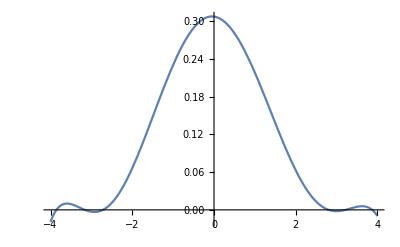

```mathematica
Plot[a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7/.{a->0.30763494607735736,b->-0.009098293833282986,c->-0.09145051419545983,d->0.003347250407987035,e->0.008744559788333687,f->-0.00037166830765117897,g->-0.0002679598507995216,h->0.000012657105993860454},{x,-4,4}]
```

```mathematica
f[x_]=a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7/.{a->0.30763494607735736,b->-0.009098293833282986,c->-0.09145051419545983,d->0.003347250407987035,e->0.008744559788333687,f->-0.00037166830765117897,g->-0.0002679598507995216,h->0.000012657105993860454}
```

0.307635-0.00909829 x-0.0914505 x^2+0.00334725 x^3+0.00874456 x^4-0.000371668 x^5-0.00026796 x^6+0.0000126571 x^7

```mathematica
f[-4]
```

-0.0191461

```mathematica
f[4]
```

-0.009913

```mathematica
Integrate[a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+0.01914605245805734/.{a->0.30763494607735736,b->-0.009098293833282986,c->-0.09145051419545983,d->0.003347250407987035,e->0.008744559788333687,f->-0.00037166830765117897,g->-0.0002679598507995216,h->0.000012657105993860454},{x,-4,4}]
```

1.03977

```mathematica
f7[x_]=(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+0.01914605245805734)/1.0397727303405975/.{a->0.30763494607735736,b->-0.009098293833282986,c->-0.09145051419545983,d->0.003347250407987035,e->0.008744559788333687,f->-0.00037166830765117897,g->-0.0002679598507995216,h->0.000012657105993860454}
```

0.961749 (0.326781-0.00909829 x-0.0914505 x^2+0.00334725 x^3+0.00874456 x^4-0.000371668 x^5-0.00026796 x^6+0.0000126571 x^7)

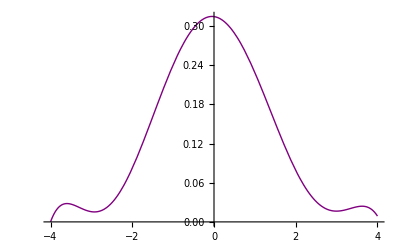

```mathematica
Plot[f7[x],{x,-4,4},PlotStyle->{Purple,Thin}]
```

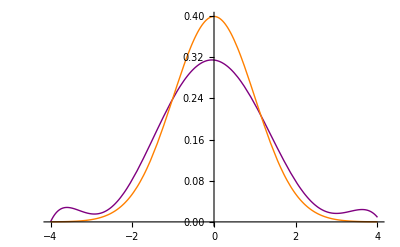

```mathematica
Plot[{f7[x],PDF[NormalDistribution[0,1],x]},{x,-4,4},PlotStyle->{{Purple,Thin},{Orange,Thin}}]
```

```mathematica
(*Divergencia de Kullback-Leibler*)
```

```mathematica
KL7= N[Integrate[F[x]*Log[F[x]/f7[x]],{x,-4,4}]]
```

0.0561008

```mathematica
(*Verosimilitud*)
```

```mathematica
x7 = Log[f7[data]]
```

{-1.2169,-1.1569,-1.9299,-1.9274,-3.80793,-1.65435,-1.48531,-1.16717,-1.16341,-2.02399,-1.15882,-1.17032,-1.43594,-1.33352,9972,-1.28474,-1.22514,-1.54611,-1.18103,-1.52117,-1.34563,-1.18181,-1.53566,-1.15981,-1.50558,-1.52392,-1.20185,-1.44752,-1.18911}
 |  |  |  |

```mathematica
V7 = Apply[Plus,x7]
```

-14721.9

```mathematica
(*BIC*)
```

```mathematica
BIC7 = -2*V7 + 8*Log[10000]
```

29517.4

### MOP DE GRADO 9

```mathematica
(*Momentos poblacionales*)
```

```mathematica
Integrate[x*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9),{x,-4,4}]
```

(128 b)/3+(2048 d)/5+(32768 f)/7+(524288 h)/9+(8388608 j)/11

```mathematica
Integrate[x^2*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9),{x,-4,4}]
```

(128 a)/3+(2048 c)/5+(32768 e)/7+(524288 g)/9+(8388608 i)/11

```mathematica
Integrate[x^3*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9),{x,-4,4}]
```

(2048 b)/5+(32768 d)/7+(524288 f)/9+(8388608 h)/11+(134217728 j)/13

```mathematica
Integrate[x^4*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9),{x,-4,4}]
```

(2048 a)/5+(32768 c)/7+(524288 e)/9+(8388608 g)/11+(134217728 i)/13

```mathematica
Integrate[x^5*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9),{x,-4,4}]
```

(32768 b)/7+(524288 d)/9+(8388608 f)/11+(134217728 h)/13+(2147483648 j)/15

```mathematica
Integrate[x^6*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9),{x,-4,4}]
```

(32768 a)/7+(524288 c)/9+(8388608 e)/11+(134217728 g)/13+(2147483648 i)/15

```mathematica
Integrate[x^7*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9),{x,-4,4}]
```

(524288 b)/9+(8388608 d)/11+(134217728 f)/13+(2147483648 h)/15+(34359738368 j)/17

```mathematica
Integrate[x^8*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9),{x,-4,4}]
```

(524288 a)/9+(8388608 c)/11+(134217728 e)/13+(2147483648 g)/15+(34359738368 i)/17

```mathematica
Integrate[x^9*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9),{x,-4,4}]
```

(8388608 b)/11+(134217728 d)/13+(2147483648 f)/15+(34359738368 h)/17+(549755813888 j)/19

```mathematica
Integrate[x^10*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9),{x,-4,4}]
```

(8388608 a)/11+(134217728 c)/13+(2147483648 e)/15+(34359738368 g)/17+(549755813888 i)/19

```mathematica
(*Solución del sistema*)
```

```mathematica
Solve[{(128 b)/3+(2048 d)/5+(32768 f)/7+(524288 h)/9+(8388608 j)/11==(Apply[Plus,data])/(10^4),(128 a)/3+(2048 c)/5+(32768 e)/7+(524288 g)/9+(8388608 i)/11==(Apply[Plus,data^2])/(10^4),(2048 b)/5+(32768 d)/7+(524288 f)/9+(8388608 h)/11+(134217728 j)/13==(Apply[Plus,data^3])/(10^4),(2048 a)/5+(32768 c)/7+(524288 e)/9+(8388608 g)/11+(134217728 i)/13==(Apply[Plus,data^4])/(10^4),(32768 b)/7+(524288 d)/9+(8388608 f)/11+(134217728 h)/13+(2147483648 j)/15==(Apply[Plus,data^5])/(10^4),(32768 a)/7+(524288 c)/9+(8388608 e)/11+(134217728 g)/13+(2147483648 i)/15==(Apply[Plus,data^6])/(10^4),(524288 b)/9+(8388608 d)/11+(134217728 f)/13+(2147483648 h)/15+(34359738368 j)/17==(Apply[Plus,data^7])/(10^4),(524288 a)/9+(8388608 c)/11+(134217728 e)/13+(2147483648 g)/15+(34359738368 i)/17==(Apply[Plus,data^8])/(10^4),(8388608 b)/11+(134217728 d)/13+(2147483648 f)/15+(34359738368 h)/17+(549755813888 j)/19==(Apply[Plus,data^9])/(10^4),(8388608 a)/11+(134217728 c)/13+(2147483648 e)/15+(34359738368 g)/17+(549755813888 i)/19==(Apply[Plus,data^10])/(10^4)},{a,b,c,d,e,f,g,h,i,j}]
```

{{a→0.362437,b→-0.0140022,c→-0.141686,d→0.00784246,e→0.0209895,f→-0.00146738,g→-0.00136126,h→0.000110488,i→0.0000322674,j→-2.88737×10^-6}}

```mathematica
(*Obtención de la función de densidad y representación gráfica*)
```

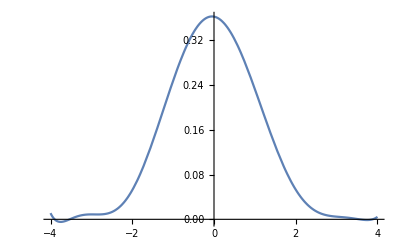

```mathematica
Plot[a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9/.{a->0.36243733537744854,b->-0.014002160197216977,c->-0.14168603772053145,d->0.007842461241592203,e->0.020989468647567983,f->-0.001467375948342276,g->-0.0013612552846596045,h->0.00011048814534126936,i->0.00003226739995767339,j->-2.887374425183713*^-6},{x,-4,4}]
```

```mathematica
F3[x_]=a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9/.{a->0.36243733537744854,b->-0.014002160197216977,c->-0.14168603772053145,d->0.007842461241592203,e->0.020989468647567983,f->-0.001467375948342276,g->-0.0013612552846596045,h->0.00011048814534126936,i->0.00003226739995767339,j->-2.887374425183713*^-6}
```

0.362437-0.0140022 x-0.141686 x^2+0.00784246 x^3+0.0209895 x^4-0.00146738 x^5-0.00136126 x^6+0.000110488 x^7+0.0000322674 x^8-2.88737×10^-6 x^9

```mathematica
Solve[F3[x]==0,Reals]
```

{{x→-3.90007},{x→-3.53052},{x→3.55764},{x→3.88032},{x→10.793}}

```mathematica
FindMinimum[F3[x],{x,-3.6}]
```

{-0.00461108,{x→-3.75186}}

```mathematica
F3[-3.7518555790318997]
```

-0.00461108

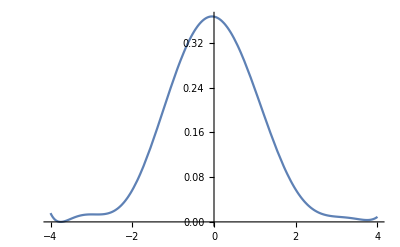

```mathematica
Plot[a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+0.004611080355509056/.{a->0.36243733537744854,b->-0.014002160197216977,c->-0.14168603772053145,d->0.007842461241592203,e->0.020989468647567983,f->-0.001467375948342276,g->-0.0013612552846596045,h->0.00011048814534126936,i->0.00003226739995767339,j->-2.887374425183713*^-6},{x,-4,4}]
```

```mathematica
F32[x_]=a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+0.004611080355509056/.{a->0.36243733537744854,b->-0.014002160197216977,c->-0.14168603772053145,d->0.007842461241592203,e->0.020989468647567983,f->-0.001467375948342276,g->-0.0013612552846596045,h->0.00011048814534126936,i->0.00003226739995767339,j->-2.887374425183713*^-6}
```

0.367048-0.0140022 x-0.141686 x^2+0.00784246 x^3+0.0209895 x^4-0.00146738 x^5-0.00136126 x^6+0.000110488 x^7+0.0000322674 x^8-2.88737×10^-6 x^9

```mathematica
Integrate[F32[x],{x,-4,4}]
```

0.995885

```mathematica
Solve[F32[x]==0,Reals]
```

{{x→-3.75186},{x→-3.75186},{x→10.793}}

```mathematica
f9[x_]=(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+0.004611080355509056)/0.9958845763001873/.{a->0.36243733537744854,b->-0.014002160197216977,c->-0.14168603772053145,d->0.007842461241592203,e->0.020989468647567983,f->-0.001467375948342276,g->-0.0013612552846596045,h->0.00011048814534126936,i->0.00003226739995767339,j->-2.887374425183713*^-6}
```

1.00413 (0.367048-0.0140022 x-0.141686 x^2+0.00784246 x^3+0.0209895 x^4-0.00146738 x^5-0.00136126 x^6+0.000110488 x^7+0.0000322674 x^8-2.88737×10^-6 x^9)

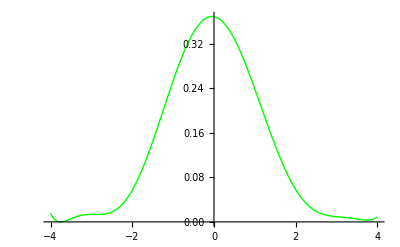

```mathematica
Plot[f9[x],{x,-4,4},PlotStyle->{Green,Thin}]
```

```mathematica
Solve[f9[x]==0,Reals]
```

{{x→-3.75186},{x→-3.75186},{x→10.793}}

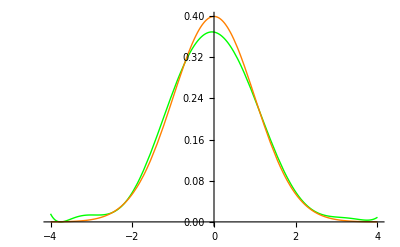

```mathematica
Plot[{f9[x],PDF[NormalDistribution[0,1],x]},{x,-4,4},PlotStyle->{{Green,Thin},{Orange,Thin}}]
```

```mathematica
(*Divergencia de Kullback-Leibler*)
```

```mathematica
KL9= N[Integrate[F[x]*Log[F[x]/f9[x]],{x,-4,4}]]
```

0.00973888

```mathematica
(*Verosimilitud*)
```

```mathematica
x9 = Log[f9[data]]
```

{-1.08073,-0.997375,-2.07894,-2.04325,-4.30739,-1.6926,-1.45561,-1.01148,-1.0063,-2.21045,-0.999995,-1.01581,-1.37924,-1.2433,9972,-1.17279,-1.09221,-1.52906,-1.03089,-1.49519,-1.2602,-1.03161,-1.51486,-1.00135,-1.48401,-1.5097,-1.05915,-1.39501,-1.04211}
 |  |  |  |

```mathematica
V9 = Apply[Plus,x9]
```

-14247.5

```mathematica
(*BIC*)
```

```mathematica
BIC9 = -2*V9 + 10*Log[10000]
```

28587.1

### MOP DE GRADO 11

```mathematica
(*Momentos poblacionales*)
```

```mathematica
Integrate[x*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11),{x,-4,4}]
```

(128 b)/3+(2048 d)/5+(32768 f)/7+(524288 h)/9+(8388608 j)/11+(134217728 l)/13

```mathematica
Integrate[x^2*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11),{x,-4,4}]
```

(128 a)/3+(2048 c)/5+(32768 e)/7+(524288 g)/9+(8388608 i)/11+(134217728 k)/13

```mathematica
Integrate[x^3*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11),{x,-4,4}]
```

(2048 b)/5+(32768 d)/7+(524288 f)/9+(8388608 h)/11+(134217728 j)/13+(2147483648 l)/15

```mathematica
Integrate[x^4*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11),{x,-4,4}]
```

(2048 a)/5+(32768 c)/7+(524288 e)/9+(8388608 g)/11+(134217728 i)/13+(2147483648 k)/15

```mathematica
Integrate[x^5*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11),{x,-4,4}]
```

(32768 b)/7+(524288 d)/9+(8388608 f)/11+(134217728 h)/13+(2147483648 j)/15+(34359738368 l)/17

```mathematica
Integrate[x^6*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11),{x,-4,4}]
```

(32768 a)/7+(524288 c)/9+(8388608 e)/11+(134217728 g)/13+(2147483648 i)/15+(34359738368 k)/17

```mathematica
Integrate[x^7*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11),{x,-4,4}]
```

(524288 b)/9+(8388608 d)/11+(134217728 f)/13+(2147483648 h)/15+(34359738368 j)/17+(549755813888 l)/19

```mathematica
Integrate[x^8*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11),{x,-4,4}]
```

(524288 a)/9+(8388608 c)/11+(134217728 e)/13+(2147483648 g)/15+(34359738368 i)/17+(549755813888 k)/19

```mathematica
Integrate[x^9*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11),{x,-4,4}]
```

(8388608 b)/11+(134217728 d)/13+(2147483648 f)/15+(34359738368 h)/17+(549755813888 j)/19+(8796093022208 l)/21

```mathematica
Integrate[x^10*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11),{x,-4,4}]
```

(8388608 a)/11+(134217728 c)/13+(2147483648 e)/15+(34359738368 g)/17+(549755813888 i)/19+(8796093022208 k)/21

```mathematica
Integrate[x^11*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11),{x,-4,4}]
```

(134217728 b)/13+(2147483648 d)/15+(34359738368 f)/17+(549755813888 h)/19+(8796093022208 j)/21+(140737488355328 l)/23

```mathematica
Integrate[x^12*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11),{x,-4,4}]
```

(134217728 a)/13+(2147483648 c)/15+(34359738368 e)/17+(549755813888 g)/19+(8796093022208 i)/21+(140737488355328 k)/23

```mathematica
(*Solución del sistema*)
```

```mathematica
Solve[{(128 b)/3+(2048 d)/5+(32768 f)/7+(524288 h)/9+(8388608 j)/11+(134217728 l)/13==(Apply[Plus,data])/(10^4),(128 a)/3+(2048 c)/5+(32768 e)/7+(524288 g)/9+(8388608 i)/11+(134217728 k)/13==(Apply[Plus,data^2])/(10^4),(2048 b)/5+(32768 d)/7+(524288 f)/9+(8388608 h)/11+(134217728 j)/13+(2147483648 l)/15==(Apply[Plus,data^3])/(10^4),(2048 a)/5+(32768 c)/7+(524288 e)/9+(8388608 g)/11+(134217728 i)/13+(2147483648 k)/15==(Apply[Plus,data^4])/(10^4),(32768 b)/7+(524288 d)/9+(8388608 f)/11+(134217728 h)/13+(2147483648 j)/15+(34359738368 l)/17==(Apply[Plus,data^5])/(10^4),(32768 a)/7+(524288 c)/9+(8388608 e)/11+(134217728 g)/13+(2147483648 i)/15+(34359738368 k)/17==(Apply[Plus,data^6])/(10^4),(524288 b)/9+(8388608 d)/11+(134217728 f)/13+(2147483648 h)/15+(34359738368 j)/17+(549755813888 l)/19==(Apply[Plus,data^7])/(10^4),(524288 a)/9+(8388608 c)/11+(134217728 e)/13+(2147483648 g)/15+(34359738368 i)/17+(549755813888 k)/19==(Apply[Plus,data^8])/(10^4),(8388608 b)/11+(134217728 d)/13+(2147483648 f)/15+(34359738368 h)/17+(549755813888 j)/19+(8796093022208 l)/21==(Apply[Plus,data^9])/(10^4),(8388608 a)/11+(134217728 c)/13+(2147483648 e)/15+(34359738368 g)/17+(549755813888 i)/19+(8796093022208 k)/21==(Apply[Plus,data^10])/(10^4),(134217728 b)/13+(2147483648 d)/15+(34359738368 f)/17+(549755813888 h)/19+(8796093022208 j)/21+(140737488355328 l)/23==(Apply[Plus,data^11])/(10^4),(134217728 a)/13+(2147483648 c)/15+(34359738368 e)/17+(549755813888 g)/19+(8796093022208 i)/21+(140737488355328 k)/23==(Apply[Plus,data^12])/(10^4)},{a,b,c,d,e,f,g,h,i,j,k,l}]
```

{{a→0.391395,b→-0.0170252,c→-0.180899,d→0.0119362,e→0.0356944,f→-0.00300254,g→-0.00359325,h→0.000343504,i→0.000179517,j→-0.0000182599,k→-3.51391×10^-6,l→3.66845×10^-7}}

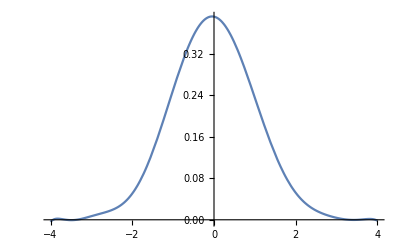

```mathematica
Plot[a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11/.{a->0.39139465752990926,b->-0.017025244786972975,c->-0.18089907813507755,d->0.011936221623526175,e->0.035694358802961956,f->-0.0030025360915607526,g->-0.003593247540382479,h->0.000343503524221916,i->0.00017951688905017726,j->-0.00001825991678185704,k->-3.5139082624287347*^-6,l->3.6684476078358317*^-7},{x,-4,4}]
```

```mathematica
f[x_]=a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11/.{a->0.39139465752990926,b->-0.017025244786972975,c->-0.18089907813507755,d->0.011936221623526175,e->0.035694358802961956,f->-0.0030025360915607526,g->-0.003593247540382479,h->0.000343503524221916,i->0.00017951688905017726,j->-0.00001825991678185704,k->-3.5139082624287347*^-6,l->3.6684476078358317*^-7}
```

0.391395-0.0170252 x-0.180899 x^2+0.0119362 x^3+0.0356944 x^4-0.00300254 x^5-0.00359325 x^6+0.000343504 x^7+0.000179517 x^8-0.0000182599 x^9-3.51391×10^-6 x^10+3.66845×10^-7 x^11

```mathematica
Solve[f[x]==0,Reals]
```

{{x→-3.93876},{x→-3.6161},{x→-3.36486},{x→3.31449},{x→3.52891},{x→3.94892},{x→9.46797}}

```mathematica
FindMinimum[f[x],{x,-3.6}]
```

{-0.000699088,{x→-3.48981}}

```mathematica
FindMinimum[f[x],{x,3.6}]
```

{-0.000276427,{x→3.42}}

```mathematica
f[-4]
```

-0.0040705

```mathematica
-0.004070504393702379
```

```mathematica
f[4]
```

-0.00184488

```mathematica
Integrate[a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+0.004070504393702379/.{a->0.39139465752990926,b->-0.017025244786972975,c->-0.18089907813507755,d->0.011936221623526175,e->0.035694358802961956,f->-0.0030025360915607526,g->-0.003593247540382479,h->0.000343503524221916,i->0.00017951688905017726,j->-0.00001825991678185704,k->-3.5139082624287347*^-6,l->3.6684476078358317*^-7},{x,-4,4}]
```

1.02317

```mathematica
f11[x_]=(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+0.004070504393702379)/1.023172687251126/.{a->0.39139465752990926,b->-0.017025244786972975,c->-0.18089907813507755,d->0.011936221623526175,e->0.035694358802961956,f->-0.0030025360915607526,g->-0.003593247540382479,h->0.000343503524221916,i->0.00017951688905017726,j->-0.00001825991678185704,k->-3.5139082624287347*^-6,l->3.6684476078358317*^-7}
```

0.977352 (0.395465-0.0170252 x-0.180899 x^2+0.0119362 x^3+0.0356944 x^4-0.00300254 x^5-0.00359325 x^6+0.000343504 x^7+0.000179517 x^8-0.0000182599 x^9-3.51391×10^-6 x^10+3.66845×10^-7 x^11)

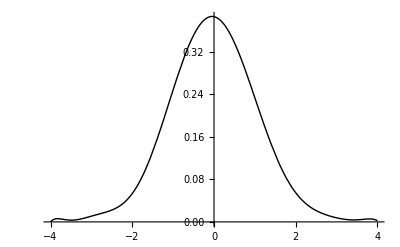

```mathematica
Plot[f11[x],{x,-4,4},PlotStyle->{Black,Thin}]
```

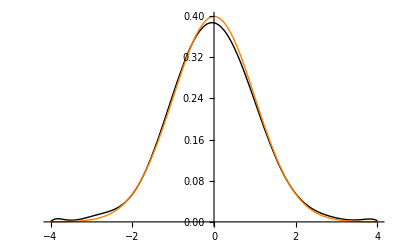

```mathematica
Plot[{f11[x],PDF[NormalDistribution[0,1],x]},{x,-4,4},PlotStyle->{{Black,Thin},{Orange,Thin}}]
```

```mathematica
(*Divergencia de Kullback-Leibler*)
```

```mathematica
KL11= N[Integrate[F[x]*Log[F[x]/f11[x]],{x,-4,4}]]
```

0.00628289

```mathematica
(*Verosimilitud*)
```

```mathematica
f11[data]
```

{0.350115,0.386799,0.113685,0.120114,0.0151283,0.172839,0.226008,0.380566,0.382874,0.0991895,0.385688,0.378642,0.248513,0.289064,9972,0.315192,0.345381,0.209788,0.371514,0.217924,0.283405,0.3717,0.213157,0.385084,0.218776,0.212452,0.359895,0.244089,0.366572}
 |  |  |  |

```mathematica
x11=Log[f11[data]]
```

{-1.04949,-0.94985,-2.17432,-2.11931,-4.19119,-1.75539,-1.48719,-0.966096,-0.960049,-2.31072,-0.952725,-0.971163,-1.39226,-1.24111,9972,-1.15457,-1.06311,-1.56166,-0.99017,-1.52361,-1.26088,-0.989667,-1.54572,-0.954294,-1.5197,-1.54904,-1.02194,-1.41022,-1.00356}
 |  |  |  |

```mathematica
V11=Apply[Plus,x11]
```

-14206.

```mathematica
(*BIC*)
```

```mathematica
BIC11 = -2*V11 + 12*Log[10000]
```

28522.6

### MOP DE GRADO 13

```mathematica
(*Momentos poblacionales*)
```

```mathematica
Integrate[x*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13),{x,-4,4}]
```

(128 b)/3+(2048 d)/5+(32768 f)/7+(524288 h)/9+(8388608 j)/11+(134217728 l)/13+(2147483648 n)/15

```mathematica
Integrate[x^2*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13),{x,-4,4}]
```

(128 a)/3+(2048 c)/5+(32768 e)/7+(524288 g)/9+(8388608 i)/11+(134217728 k)/13+(2147483648 m)/15

```mathematica
Integrate[x^3*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13),{x,-4,4}]
```

(2048 b)/5+(32768 d)/7+(524288 f)/9+(8388608 h)/11+(134217728 j)/13+(2147483648 l)/15+(34359738368 n)/17

```mathematica
Integrate[x^4*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13),{x,-4,4}]
```

(2048 a)/5+(32768 c)/7+(524288 e)/9+(8388608 g)/11+(134217728 i)/13+(2147483648 k)/15+(34359738368 m)/17

```mathematica
Integrate[x^5*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13),{x,-4,4}]
```

(32768 b)/7+(524288 d)/9+(8388608 f)/11+(134217728 h)/13+(2147483648 j)/15+(34359738368 l)/17+(549755813888 n)/19

```mathematica
Integrate[x^6*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13),{x,-4,4}]
```

(32768 a)/7+(524288 c)/9+(8388608 e)/11+(134217728 g)/13+(2147483648 i)/15+(34359738368 k)/17+(549755813888 m)/19

```mathematica
Integrate[x^7*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13),{x,-4,4}]
```

(524288 b)/9+(8388608 d)/11+(134217728 f)/13+(2147483648 h)/15+(34359738368 j)/17+(549755813888 l)/19+(8796093022208 n)/21

```mathematica
Integrate[x^8*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13),{x,-4,4}]
```

(524288 a)/9+(8388608 c)/11+(134217728 e)/13+(2147483648 g)/15+(34359738368 i)/17+(549755813888 k)/19+(8796093022208 m)/21

```mathematica
Integrate[x^9*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13),{x,-4,4}]
```

(8388608 b)/11+(134217728 d)/13+(2147483648 f)/15+(34359738368 h)/17+(549755813888 j)/19+(8796093022208 l)/21+(140737488355328 n)/23

```mathematica
Integrate[x^10*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13),{x,-4,4}]
```

(8388608 a)/11+(134217728 c)/13+(2147483648 e)/15+(34359738368 g)/17+(549755813888 i)/19+(8796093022208 k)/21+(140737488355328 m)/23

```mathematica
Integrate[x^11*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13),{x,-4,4}]
```

(134217728 b)/13+(2147483648 d)/15+(34359738368 f)/17+(549755813888 h)/19+(8796093022208 j)/21+(140737488355328 l)/23+(2251799813685248 n)/25

```mathematica
Integrate[x^12*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13),{x,-4,4}]
```

(134217728 a)/13+(2147483648 c)/15+(34359738368 e)/17+(549755813888 g)/19+(8796093022208 i)/21+(140737488355328 k)/23+(2251799813685248 m)/25

```mathematica
Integrate[x^13*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13),{x,-4,4}]
```

(2147483648 b)/15+(34359738368 d)/17+(549755813888 f)/19+(8796093022208 h)/21+(140737488355328 j)/23+(2251799813685248 l)/25+(36028797018963968 n)/27

```mathematica
Integrate[x^14*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13),{x,-4,4}]
```

(2147483648 a)/15+(34359738368 c)/17+(549755813888 e)/19+(8796093022208 g)/21+(140737488355328 i)/23+(2251799813685248 k)/25+(36028797018963968 m)/27

```mathematica
(*Solución del sistema*)
```

```mathematica
NSolve[{(128 b)/3+(2048 d)/5+(32768 f)/7+(524288 h)/9+(8388608 j)/11+(134217728 l)/13+(2147483648 n)/15==(Apply[Plus,data])/(10^4),(128 a)/3+(2048 c)/5+(32768 e)/7+(524288 g)/9+(8388608 i)/11+(134217728 k)/13+(2147483648 m)/15==(Apply[Plus,data^2])/(10^4),(2048 b)/5+(32768 d)/7+(524288 f)/9+(8388608 h)/11+(134217728 j)/13+(2147483648 l)/15+(34359738368 n)/17==(Apply[Plus,data^3])/(10^4),(2048 a)/5+(32768 c)/7+(524288 e)/9+(8388608 g)/11+(134217728 i)/13+(2147483648 k)/15+(34359738368 m)/17==(Apply[Plus,data^4])/(10^4),(32768 b)/7+(524288 d)/9+(8388608 f)/11+(134217728 h)/13+(2147483648 j)/15+(34359738368 l)/17+(549755813888 n)/19==(Apply[Plus,data^5])/(10^4),(32768 a)/7+(524288 c)/9+(8388608 e)/11+(134217728 g)/13+(2147483648 i)/15+(34359738368 k)/17+(549755813888 m)/19==(Apply[Plus,data^6])/(10^4),(524288 b)/9+(8388608 d)/11+(134217728 f)/13+(2147483648 h)/15+(34359738368 j)/17+(549755813888 l)/19+(8796093022208 n)/21==(Apply[Plus,data^7])/(10^4),(524288 a)/9+(8388608 c)/11+(134217728 e)/13+(2147483648 g)/15+(34359738368 i)/17+(549755813888 k)/19+(8796093022208 m)/21==(Apply[Plus,data^8])/(10^4),(8388608 b)/11+(134217728 d)/13+(2147483648 f)/15+(34359738368 h)/17+(549755813888 j)/19+(8796093022208 l)/21+(140737488355328 n)/23==(Apply[Plus,data^9])/(10^4),(8388608 a)/11+(134217728 c)/13+(2147483648 e)/15+(34359738368 g)/17+(549755813888 i)/19+(8796093022208 k)/21+(140737488355328 m)/23==(Apply[Plus,data^10])/(10^4),(134217728 b)/13+(2147483648 d)/15+(34359738368 f)/17+(549755813888 h)/19+(8796093022208 j)/21+(140737488355328 l)/23+(2251799813685248 n)/25==(Apply[Plus,data^11])/(10^4),(134217728 a)/13+(2147483648 c)/15+(34359738368 e)/17+(549755813888 g)/19+(8796093022208 i)/21+(140737488355328 k)/23+(2251799813685248 m)/25==(Apply[Plus,data^12])/(10^4),(2147483648 b)/15+(34359738368 d)/17+(549755813888 f)/19+(8796093022208 h)/21+(140737488355328 j)/23+(2251799813685248 l)/25+(36028797018963968 n)/27==(Apply[Plus,data^13])/(10^4),(2147483648 a)/15+(34359738368 c)/17+(549755813888 e)/19+(8796093022208 g)/21+(140737488355328 i)/23+(2251799813685248 k)/25+(36028797018963968 m)/27==(Apply[Plus,data^14])/(10^4)},{a,b,c,d,e,f,g,h,i,j,k,l,m,n}]
```

{{a→0.40473,b→-0.0147144,c→-0.205903,d→0.00760346,e→0.0489777,f→-0.000700755,g→-0.00659782,h→-0.000177137,i→0.000508142,j→0.0000386852,k→-0.000020692,l→-2.60983×10^-6,m→3.44113×10^-7,n→5.96289×10^-8}}

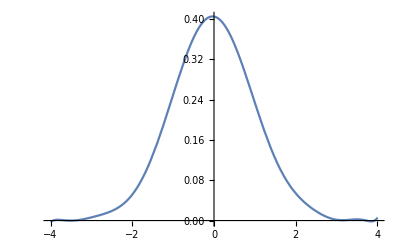

```mathematica
Plot[a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13/.{a->0.4047301110498327,b->-0.014714437357997904,c->-0.20590305348266344,d->0.007603457694713388,e->0.04897772070553385,f->-0.0007007552545621098,g->-0.006597817494397705,h->-0.00017713737935520898,i->0.00050814172775906,j->0.000038685182044442664,k->-0.000020692024830826097,l->-2.609830859582113*^-6,m->3.4411291201946673*^-7,n->5.962891867558906*^-8},{x,-4,4}]
```

```mathematica
(*Obtención de la densidad y representación gráfica*)
```

```mathematica
f[x_]=a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13/.{a->0.4047301110498327,b->-0.014714437357997904,c->-0.20590305348266344,d->0.007603457694713388,e->0.04897772070553385,f->-0.0007007552545621098,g->-0.006597817494397705,h->-0.00017713737935520898,i->0.00050814172775906,j->0.000038685182044442664,k->-0.000020692024830826097,l->-2.609830859582113*^-6,m->3.4411291201946673*^-7,n->5.962891867558906*^-8}
```

0.40473-0.0147144 x-0.205903 x^2+0.00760346 x^3+0.0489777 x^4-0.000700755 x^5-0.00659782 x^6-0.000177137 x^7+0.000508142 x^8+0.0000386852 x^9-0.000020692 x^10-2.60983×10^-6 x^11+3.44113×10^-7 x^12+5.96289×10^-8 x^13

```mathematica
f[-4]
```

-0.00267509

```mathematica
FindMinimum[f[x],{x,3.5}]
```

{-0.0016481,{x→3.84983}}

```mathematica
Integrate[a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13+0.0026750874192416063/.{a->0.4047301110498327,b->-0.014714437357997904,c->-0.20590305348266344,d->0.007603457694713388,e->0.04897772070553385,f->-0.0007007552545621098,g->-0.006597817494397705,h->-0.00017713737935520898,i->0.00050814172775906,j->0.000038685182044442664,k->-0.000020692024830826097,l->-2.609830859582113*^-6,m->3.4411291201946673*^-7,n->5.962891867558906*^-8},{x,-4,4}]
```

1.02441

```mathematica
f13[x_]=(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13+0.0026750874192416063)/1.02441407317259/.{a->0.4047301110498327,b->-0.014714437357997904,c->-0.20590305348266344,d->0.007603457694713388,e->0.04897772070553385,f->-0.0007007552545621098,g->-0.006597817494397705,h->-0.00017713737935520898,i->0.00050814172775906,j->0.000038685182044442664,k->-0.000020692024830826097,l->-2.609830859582113*^-6,m->3.4411291201946673*^-7,n->5.962891867558906*^-8}
```

0.976168 (0.407405-0.0147144 x-0.205903 x^2+0.00760346 x^3+0.0489777 x^4-0.000700755 x^5-0.00659782 x^6-0.000177137 x^7+0.000508142 x^8+0.0000386852 x^9-0.000020692 x^10-2.60983×10^-6 x^11+3.44113×10^-7 x^12+5.96289×10^-8 x^13)

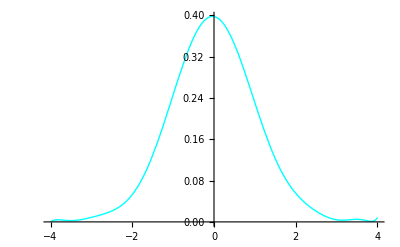

```mathematica
Plot[f13[x],{x,-4,4},PlotStyle->{Cyan,Thin}]
```

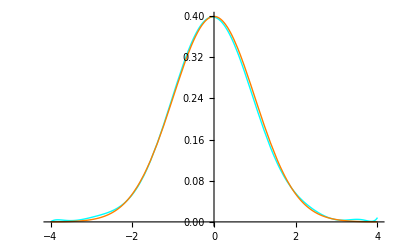

```mathematica
Plot[{f13[x],PDF[NormalDistribution[0,1],x]},{x,-4,4},PlotStyle->{{Cyan,Thin},{Orange,Thin}}]
```

```mathematica
(*Divergencia de Kullback-Leibler*)
```

```mathematica
KL13= N[Integrate[F[x]*Log[F[x]/f13[x]],{x,-4,4}]]
```

0.00378639

```mathematica
(*Verosimilitud*)
```

```mathematica
x13=Log[f13[data]]
```

{-1.0351,-0.922041,-2.19872,-2.15498,-4.37363,-1.77797,-1.50183,-0.937573,-0.931321,-2.3335,-0.924006,-0.942875,-1.39985,-1.24252,9972,-1.14143,-1.05007,-1.58162,-0.96911,-1.54103,-1.26361,-0.962496,-1.56464,-0.925527,-1.53564,-1.56606,-0.997177,-1.41925,-0.984142}
 |  |  |  |

```mathematica
V13=Apply[Plus,x13]
```

-14179.8

```mathematica
(*BIC*)
```

```mathematica
BIC13 = -2*V13 + 14*Log[10000]
```

28488.5

### MOP DE GRADO 15

```mathematica
(*Momentos poblacionales*)
```

```mathematica
Integrate[x*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13+o*x^14+p*x^15),{x,-4,4}]
```

(128 b)/3+(2048 d)/5+(32768 f)/7+(524288 h)/9+(8388608 j)/11+(134217728 l)/13+(2147483648 n)/15+(34359738368 p)/17

```mathematica
Integrate[x^2*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13+o*x^14+p*x^15),{x,-4,4}]
```

(128 a)/3+(2048 c)/5+(32768 e)/7+(524288 g)/9+(8388608 i)/11+(134217728 k)/13+(2147483648 m)/15+(34359738368 o)/17

```mathematica
Integrate[x^3*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13+o*x^14+p*x^15),{x,-4,4}]
```

(2048 b)/5+(32768 d)/7+(524288 f)/9+(8388608 h)/11+(134217728 j)/13+(2147483648 l)/15+(34359738368 n)/17+(549755813888 p)/19

```mathematica
Integrate[x^4*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13+o*x^14+p*x^15),{x,-4,4}]
```

(2048 a)/5+(32768 c)/7+(524288 e)/9+(8388608 g)/11+(134217728 i)/13+(2147483648 k)/15+(34359738368 m)/17+(549755813888 o)/19

```mathematica
Integrate[x^5*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13+o*x^14+p*x^15),{x,-4,4}]
```

(32768 b)/7+(524288 d)/9+(8388608 f)/11+(134217728 h)/13+(2147483648 j)/15+(34359738368 l)/17+(549755813888 n)/19+(8796093022208 p)/21

```mathematica
Integrate[x^6*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13+o*x^14+p*x^15),{x,-4,4}]
```

(32768 a)/7+(524288 c)/9+(8388608 e)/11+(134217728 g)/13+(2147483648 i)/15+(34359738368 k)/17+(549755813888 m)/19+(8796093022208 o)/21

```mathematica
Integrate[x^7*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13+o*x^14+p*x^15),{x,-4,4}]
```

(524288 b)/9+(8388608 d)/11+(134217728 f)/13+(2147483648 h)/15+(34359738368 j)/17+(549755813888 l)/19+(8796093022208 n)/21+(140737488355328 p)/23

```mathematica
Integrate[x^8*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13+o*x^14+p*x^15),{x,-4,4}]
```

(524288 a)/9+(8388608 c)/11+(134217728 e)/13+(2147483648 g)/15+(34359738368 i)/17+(549755813888 k)/19+(8796093022208 m)/21+(140737488355328 o)/23

```mathematica
Integrate[x^9*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13+o*x^14+p*x^15),{x,-4,4}]
```

(8388608 b)/11+(134217728 d)/13+(2147483648 f)/15+(34359738368 h)/17+(549755813888 j)/19+(8796093022208 l)/21+(140737488355328 n)/23+(2251799813685248 p)/25

```mathematica
Integrate[x^10*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13+o*x^14+p*x^15),{x,-4,4}]
```

(8388608 a)/11+(134217728 c)/13+(2147483648 e)/15+(34359738368 g)/17+(549755813888 i)/19+(8796093022208 k)/21+(140737488355328 m)/23+(2251799813685248 o)/25

```mathematica
Integrate[x^11*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13+o*x^14+p*x^15),{x,-4,4}]
```

(134217728 b)/13+(2147483648 d)/15+(34359738368 f)/17+(549755813888 h)/19+(8796093022208 j)/21+(140737488355328 l)/23+(2251799813685248 n)/25+(36028797018963968 p)/27

```mathematica
Integrate[x^12*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13+o*x^14+p*x^15),{x,-4,4}]
```

(134217728 a)/13+(2147483648 c)/15+(34359738368 e)/17+(549755813888 g)/19+(8796093022208 i)/21+(140737488355328 k)/23+(2251799813685248 m)/25+(36028797018963968 o)/27

```mathematica
Integrate[x^13*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13+o*x^14+p*x^15),{x,-4,4}]
```

(2147483648 b)/15+(34359738368 d)/17+(549755813888 f)/19+(8796093022208 h)/21+(140737488355328 j)/23+(2251799813685248 l)/25+(36028797018963968 n)/27+(576460752303423488 p)/29

```mathematica
Integrate[x^14*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13+o*x^14+p*x^15),{x,-4,4}]
```

(2147483648 a)/15+(34359738368 c)/17+(549755813888 e)/19+(8796093022208 g)/21+(140737488355328 i)/23+(2251799813685248 k)/25+(36028797018963968 m)/27+(576460752303423488 o)/29

```mathematica
Integrate[x^15*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13+o*x^14+p*x^15),{x,-4,4}]
```

(34359738368 b)/17+(549755813888 d)/19+(8796093022208 f)/21+(140737488355328 h)/23+(2251799813685248 j)/25+(36028797018963968 l)/27+(576460752303423488 n)/29+(9223372036854775808 p)/31

```mathematica
Integrate[x^16*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13+o*x^14+p*x^15),{x,-4,4}]
```

(34359738368 a)/17+(549755813888 c)/19+(8796093022208 e)/21+(140737488355328 g)/23+(2251799813685248 i)/25+(36028797018963968 k)/27+(576460752303423488 m)/29+(9223372036854775808 o)/31

```mathematica
(*Solución del sistema*)
```

```mathematica
NSolve[{(128 b)/3+(2048 d)/5+(32768 f)/7+(524288 h)/9+(8388608 j)/11+(134217728 l)/13+(2147483648 n)/15+(34359738368 p)/17==(Apply[Plus,data])/(10^4),(128 a)/3+(2048 c)/5+(32768 e)/7+(524288 g)/9+(8388608 i)/11+(134217728 k)/13+(2147483648 m)/15+(34359738368 o)/17==(Apply[Plus,data^2])/(10^4),(2048 b)/5+(32768 d)/7+(524288 f)/9+(8388608 h)/11+(134217728 j)/13+(2147483648 l)/15+(34359738368 n)/17+(549755813888 p)/19==(Apply[Plus,data^3])/(10^4),(2048 a)/5+(32768 c)/7+(524288 e)/9+(8388608 g)/11+(134217728 i)/13+(2147483648 k)/15+(34359738368 m)/17+(549755813888 o)/19==(Apply[Plus,data^4])/(10^4),(32768 b)/7+(524288 d)/9+(8388608 f)/11+(134217728 h)/13+(2147483648 j)/15+(34359738368 l)/17+(549755813888 n)/19+(8796093022208 p)/21==(Apply[Plus,data^5])/(10^4),(32768 a)/7+(524288 c)/9+(8388608 e)/11+(134217728 g)/13+(2147483648 i)/15+(34359738368 k)/17+(549755813888 m)/19+(8796093022208 o)/21==(Apply[Plus,data^6])/(10^4),(524288 b)/9+(8388608 d)/11+(134217728 f)/13+(2147483648 h)/15+(34359738368 j)/17+(549755813888 l)/19+(8796093022208 n)/21+(140737488355328 p)/23==(Apply[Plus,data^7])/(10^4),(524288 a)/9+(8388608 c)/11+(134217728 e)/13+(2147483648 g)/15+(34359738368 i)/17+(549755813888 k)/19+(8796093022208 m)/21+(140737488355328 o)/23==(Apply[Plus,data^8])/(10^4),(8388608 b)/11+(134217728 d)/13+(2147483648 f)/15+(34359738368 h)/17+(549755813888 j)/19+(8796093022208 l)/21+(140737488355328 n)/23+(2251799813685248 p)/25==(Apply[Plus,data^9])/(10^4),(8388608 a)/11+(134217728 c)/13+(2147483648 e)/15+(34359738368 g)/17+(549755813888 i)/19+(8796093022208 k)/21+(140737488355328 m)/23+(2251799813685248 o)/25==(Apply[Plus,data^10])/(10^4),(134217728 b)/13+(2147483648 d)/15+(34359738368 f)/17+(549755813888 h)/19+(8796093022208 j)/21+(140737488355328 l)/23+(2251799813685248 n)/25+(36028797018963968 p)/27==(Apply[Plus,data^11])/(10^4),(134217728 a)/13+(2147483648 c)/15+(34359738368 e)/17+(549755813888 g)/19+(8796093022208 i)/21+(140737488355328 k)/23+(2251799813685248 m)/25+(36028797018963968 o)/27==(Apply[Plus,data^12])/(10^4),(2147483648 b)/15+(34359738368 d)/17+(549755813888 f)/19+(8796093022208 h)/21+(140737488355328 j)/23+(2251799813685248 l)/25+(36028797018963968 n)/27+(576460752303423488 p)/29==(Apply[Plus,data^13])/(10^4),(2147483648 a)/15+(34359738368 c)/17+(549755813888 e)/19+(8796093022208 g)/21+(140737488355328 i)/23+(2251799813685248 k)/25+(36028797018963968 m)/27+(576460752303423488 o)/29==(Apply[Plus,data^14])/(10^4),(34359738368 b)/17+(549755813888 d)/19+(8796093022208 f)/21+(140737488355328 h)/23+(2251799813685248 j)/25+(36028797018963968 l)/27+(576460752303423488 n)/29+(9223372036854775808 p)/31==(Apply[Plus,data^15])/(10^4),(34359738368 a)/17+(549755813888 c)/19+(8796093022208 e)/21+(140737488355328 g)/23+(2251799813685248 i)/25+(36028797018963968 k)/27+(576460752303423488 m)/29+(9223372036854775808 o)/31==(Apply[Plus,data^16])/(10^4)},{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p}]
```

{{a→0.409026,b→-0.00685017,c→-0.216552,d→-0.0118934,e→0.0565654,f→0.0131907,g→-0.00896898,h→-0.00451823,i→0.000886869,j→0.000732054,k→-0.0000529699,l→-0.0000617038,m→1.74075×10^-6,n→2.61658×10^-6,o→-2.41086×10^-8,p→-4.41378×10^-8}}

```mathematica
(*Obtención de la densidad y representación*)
```

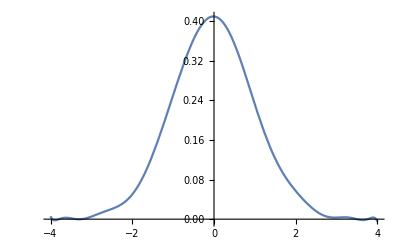

```mathematica
Plot[a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13+o*x^14+p*x^15/.{a->0.4090256741933678,b->-0.006850170305112355,c->-0.21655247045573595,d->-0.01189337104556469,e->0.05656543030673936,f->0.013190735226231862,g->-0.008968976746769946,h->-0.004518228155459072,i->0.0008868685530489301,j->0.0007320538477814404,k->-0.00005296987927696726,l->-0.00006170375124235965,m->1.7407508454327788*^-6,n->2.6165773970379608*^-6,o->-2.4108631002845782*^-8,p->-4.4137801118284036*^-8},{x,-4,4}]
```

```mathematica
F15[x_]=a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13+o*x^14+p*x^15/.{a->0.4090256741933678,b->-0.006850170305112355,c->-0.21655247045573595,d->-0.01189337104556469,e->0.05656543030673936,f->0.013190735226231862,g->-0.008968976746769946,h->-0.004518228155459072,i->0.0008868685530489301,j->0.0007320538477814404,k->-0.00005296987927696726,l->-0.00006170375124235965,m->1.7407508454327788*^-6,n->2.6165773970379608*^-6,o->-2.4108631002845782*^-8,p->-4.4137801118284036*^-8}
```

0.409026-0.00685017 x-0.216552 x^2-0.0118934 x^3+0.0565654 x^4+0.0131907 x^5-0.00896898 x^6-0.00451823 x^7+0.000886869 x^8+0.000732054 x^9-0.0000529699 x^10-0.0000617038 x^11+1.74075×10^-6 x^12+2.61658×10^-6 x^13-2.41086×10^-8 x^14-4.41378×10^-8 x^15

```mathematica
Solve[F15[x]==0,Reals]
```

{{x→-3.95689},{x→-3.79113},{x→-3.35439},{x→-3.25047},{x→3.49619},{x→3.76598},{x→3.96496}}

```mathematica
FindMinimum[F15[x],{x,-3.8}]
```

{-0.00234846,{x→-3.89348}}

```mathematica
F15[4]
```

-0.00552434

```mathematica
FindMinimum[F15[x],{x,3.5}]
```

{-0.00183543,{x→3.64361}}

```mathematica
Integrate[a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13+o*x^14+p*x^15+0.005524340563411556/.{a->0.4090256741933678,b->-0.006850170305112355,c->-0.21655247045573595,d->-0.01189337104556469,e->0.05656543030673936,f->0.013190735226231862,g->-0.008968976746769946,h->-0.004518228155459072,i->0.0008868685530489301,j->0.0007320538477814404,k->-0.00005296987927696726,l->-0.00006170375124235965,m->1.7407508454327788*^-6,n->2.6165773970379608*^-6,o->-2.4108631002845782*^-8,p->-4.4137801118284036*^-8},{x,-4,4}]
```

1.05069

```mathematica
f15[x_]=(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13+o*x^14+p*x^15+0.005524340563411556)/1.050688848842828/.{a->0.4090256741933678,b->-0.006850170305112355,c->-0.21655247045573595,d->-0.01189337104556469,e->0.05656543030673936,f->0.013190735226231862,g->-0.008968976746769946,h->-0.004518228155459072,i->0.0008868685530489301,j->0.0007320538477814404,k->-0.00005296987927696726,l->-0.00006170375124235965,m->1.7407508454327788*^-6,n->2.6165773970379608*^-6,o->-2.4108631002845782*^-8,p->-4.4137801118284036*^-8}
```

0.951757 (0.41455-0.00685017 x-0.216552 x^2-0.0118934 x^3+0.0565654 x^4+0.0131907 x^5-0.00896898 x^6-0.00451823 x^7+0.000886869 x^8+0.000732054 x^9-0.0000529699 x^10-0.0000617038 x^11+1.74075×10^-6 x^12+2.61658×10^-6 x^13-2.41086×10^-8 x^14-4.41378×10^-8 x^15)

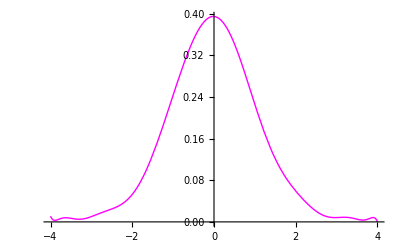

```mathematica
Plot[f15[x],{x,-4,4},PlotStyle->{Magenta,Thin}]
```

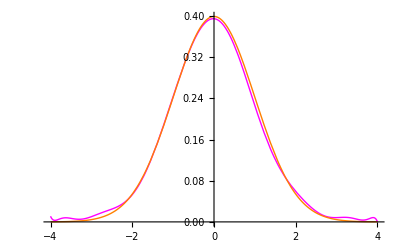

```mathematica
Plot[{f15[x],PDF[NormalDistribution[0,1],x]},{x,-4,4},PlotStyle->{{Magenta,Thin},{Orange,Thin}}]
```

```mathematica
(*Divergencia de Kullback-Leibler*)
```

```mathematica
KL15= N[Integrate[F[x]*Log[F[x]/f15[x]],{x,-4,4}]]
```

0.0089653

```mathematica
(*Verosimilitud*)
```

```mathematica
x15 = Log[f15[data]]
```

{-1.05224,-0.931432,-2.20016,-2.16055,-4.38206,-1.78087,-1.51065,-0.943155,-0.937441,-2.33614,-0.931268,-0.948136,-1.42028,-1.25806,9972,-1.15048,-1.0674,-1.60709,-0.984133,-1.56575,-1.27867,-0.967122,-1.58983,-0.932456,-1.54358,-1.57324,-1.00173,-1.44039,-0.999895}
 |  |  |  |

```mathematica
V15=Apply[Plus,x15]
```

-14225.9

```mathematica
(*BIC*)
```

```mathematica
BIC15 = -2*V15 + 16*Log[10000]
```

28599.1

### EVOLUCIÓN

```mathematica
(*Representación gráfica de todas juntas*)
```

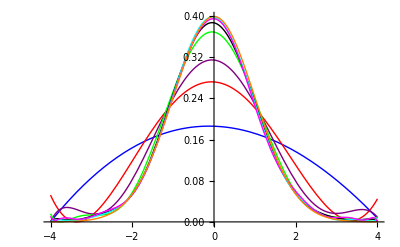

```mathematica
Plot[{f3[x],f5[x],f7[x],f9[x],f11[x],f13[x],f15[x],PDF[NormalDistribution[0,1],x]},{x,-4,4},PlotStyle->{{Blue,Thin},{Red,Thin},{Purple,Thin},{Green,Thin},{Black,Thin},{Cyan,Thin},{Magenta,Thin},{Orange,Thin}}]
```

### GRÁFICO DIVERGENCIAS

```mathematica
DKL = {{{3,0.33375270099372417}},{{5,0.09538243334051046}},{{7,0.05610079770456803}},{{9,0.009738882673900643}},{{11,0.006282892644619598}},{{13,0.0037863930049534134}},{{15,0.008965303208253488}}}
```

{{{3,0.333753}},{{5,0.0953824}},{{7,0.0561008}},{{9,0.00973888}},{{11,0.00628289}},{{13,0.00378639}},{{15,0.0089653}}}

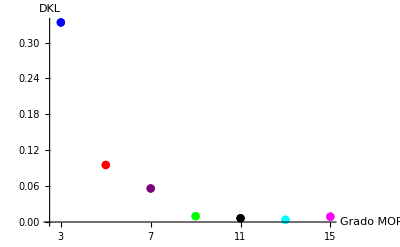

```mathematica
g1 =ListPlot[DKL,PlotStyle->{{Blue,Thin,PointSize[0.015]},{Red,Thin,PointSize[0.015]},{Purple,Thin,PointSize[0.015]},{Green,Thin,PointSize[0.015]},{Black,Thin,PointSize[0.015]},{Cyan,Thin,PointSize[0.015]},{Magenta,Thin,PointSize[0.015]}},AxesLabel->{"Grado MOP","DKL"},AxesOrigin->{2.5,0},AxesStyle->Directive[Black, 12],PlotRange->Full,Ticks->{{3,5,7,9,11,13,15}, Automatic}]
```

```mathematica
DKL1 =  {{3,0.33375270099372417},{5,0.09538243334051046},{7,0.05610079770456803},{9,0.009738882673900643},{11,0.006282892644619598},{13,0.0037863930049534134},{15,0.008965303208253488}}
```

{{3,0.333753},{5,0.0953824},{7,0.0561008},{9,0.00973888},{11,0.00628289},{13,0.00378639},{15,0.0089653}}

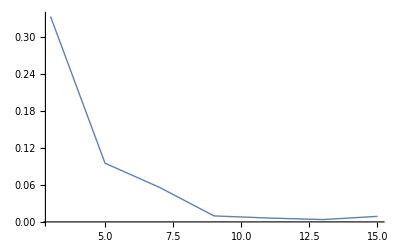

```mathematica
g2 = ListLinePlot[DKL1,PlotStyle->Thin,PlotRange->Full]
```

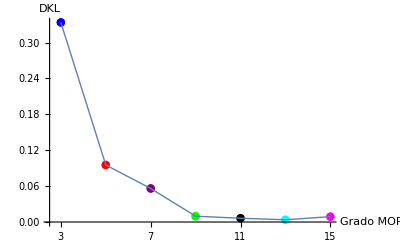

```mathematica
GrafDivM=Show[g1,g2]
```

### GRÁFICO VEROSIMILITUDES

```mathematica
V = {{{3,-17514.784540173292}},{{5,-15121.734287651721}},{{7,-14721.857621307312}},{{9,-14247.495262275885}},{{11,-14206.047516082175}},{{13,-14179.801165809093}},{{15,-14225.864102921572}}}
```

{{{3,-17514.8}},{{5,-15121.7}},{{7,-14721.9}},{{9,-14247.5}},{{11,-14206.}},{{13,-14179.8}},{{15,-14225.9}}}

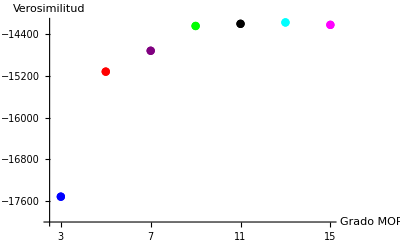

```mathematica
h1 =ListPlot[V,PlotStyle->{{Blue,Thin,PointSize[0.015]},{Red,Thin,PointSize[0.015]},{Purple,Thin,PointSize[0.015]},{Green,Thin,PointSize[0.015]},{Black,Thin,PointSize[0.015]},{Cyan,Thin,PointSize[0.015]},{Magenta,Thin,PointSize[0.015]}},AxesLabel->{"Grado MOP","Verosimilitud"},AxesOrigin->{2.5,-18000},AxesStyle->Directive[Black, 12],PlotRange->Full,Ticks->{{3,5,7,9,11,13,15}, Automatic}]
```

```mathematica
V1 ={{3,-17514.784540173292},{5,-15121.734287651721},{7,-14721.857621307312},{9,-14247.495262275885},{11,-14206.047516082175},{13,-14179.801165809093},{15,-14225.864102921572}}
```

{{3,-17514.8},{5,-15121.7},{7,-14721.9},{9,-14247.5},{11,-14206.},{13,-14179.8},{15,-14225.9}}

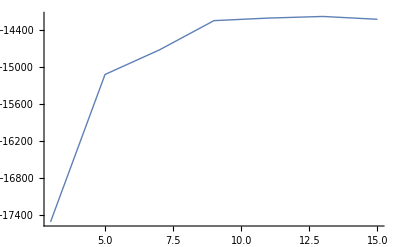

```mathematica
h2 = ListLinePlot[V1,PlotStyle->Thin,PlotRange->Full]
```

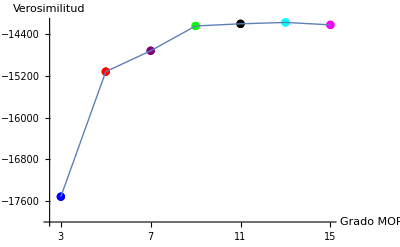

```mathematica
GrafVNMuestra1=Show[h1,h2]
```

```mathematica
(*Gráfico verosimilitudes con otra muestra*)
```

```mathematica
SeedRandom[4321]
```

```mathematica
data2 = RandomVariate[NormalDistribution[0,1],10^4]
```

{0.747051,-1.23297,0.881603,-0.0754897,-0.631166,0.511102,2.26024,-0.792594,0.443516,0.444986,0.765234,-1.37841,-0.376238,1.56308,9972,0.186956,-1.66499,0.78839,-1.00169,-0.262297,-0.431108,-0.292597,-0.477039,-0.627549,0.884375,0.424782,-0.0453317,-0.8449,0.982922}
 |  |  |  |

```mathematica
y3 = Log[f3[data2]]
```

{-1.72277,-1.75227,-1.73947,-1.67301,-1.68811,-1.69951,-2.09934,-1.70013,-1.69422,-1.69432,-1.72487,-1.77634,-1.67625,-1.86768,9972,-1.67948,-1.83526,-1.72762,-1.72121,-1.67367,-1.67808,-1.67419,-1.67992,-1.68788,-1.73984,-1.69285,-1.67331,-1.70481,-1.75378}
 |  |  |  |

```mathematica
L3 = Apply[Plus,y3]
```

-17514.4

```mathematica
y5= Log[f5[data2]]
```

{-1.41906,-1.56573,-1.46276,-1.30223,-1.36124,-1.35999,-2.52943,-1.40043,-1.347,-1.34726,-1.42453,-1.64193,-1.32009,-1.81745,9972,-1.31287,-1.83087,-1.43169,-1.46759,-1.3095,-1.32688,-1.31185,-1.33342,-1.36048,-1.46374,-1.3437,-1.30221,-1.41544,-1.50078}
 |  |  |  |

```mathematica
L5= Apply[Plus,y5]
```

-15106.7

```mathematica
y7= Log[f7[data2]]
```

{-1.33753,-1.58559,-1.40573,-1.15696,-1.25418,-1.24542,-2.99437,-1.31779,-1.2252,-1.22562,-1.34606,-1.70894,-1.18704,-1.95618,9972,-1.17247,-2.014,-1.35723,-1.42663,-1.16955,-1.19818,-1.17347,-1.20888,-1.25294,-1.40726,-1.22007,-1.15678,-1.34213,-1.46506}
 |  |  |  |

```mathematica
L7= Apply[Plus,y7]
```

-14739.1

```mathematica
y9= Log[f9[data2]]
```

{-1.24498,-1.59616,-1.33807,-0.997465,-1.13263,-1.11893,-3.4163,-1.22134,-1.09121,-1.09177,-1.25664,-1.76918,-1.03923,-2.08175,9972,-1.01876,-2.1965,-1.27189,-1.37346,-1.01494,-1.05471,-1.02038,-1.06958,-1.13091,-1.34016,-1.08417,-0.997204,-1.25532,-1.41889}
 |  |  |  |

```mathematica
L9= Apply[Plus,y9]
```

-14281.2

```mathematica
y11= Log[f11[data2]]
```

{-1.23821,-1.64715,-1.34524,-0.949968,-1.11095,-1.09185,-3.39366,-1.21538,-1.05946,-1.06012,-1.25166,-1.84038,-1.00013,-2.15942,9972,-0.974619,-2.29643,-1.26925,-1.39256,-0.9711,-1.01856,-0.977612,-1.03625,-1.10893,-1.34763,-1.05123,-0.949592,-1.25516,-1.43736}
 |  |  |  |

```mathematica
L11= Apply[Plus,y11]
```

-14249.4

```mathematica
y13= Log[f13[data2]]
```

{-1.23262,-1.66725,-1.34897,-0.922226,-1.10234,-1.07305,-3.36079,-1.21501,-1.03782,-1.03854,-1.24728,-1.86428,-0.980301,-2.19448,9972,-0.946514,-2.31942,-1.26642,-1.40288,-0.947456,-1.00087,-0.954895,-1.02048,-1.10014,-1.35156,-1.02889,-0.921471,-1.25752,-1.44851}
 |  |  |  |

```mathematica
L13= Apply[Plus,y13]
```

-14223.4

```mathematica
y15=Log[f15[data2]]
```

{-1.2458,-1.67213,-1.36735,-0.931722,-1.11983,-1.07942,-3.30103,-1.2311,-1.04313,-1.04386,-1.26113,-1.86609,-0.995886,-2.19654,9972,-0.951601,-2.32191,-1.28116,-1.41436,-0.960969,-1.01724,-0.969007,-1.03736,-1.11763,-1.37005,-1.03397,-0.930329,-1.27272,-1.47067}
 |  |  |  |

```mathematica
L15= Apply[Plus,y15]
```

-14275.8

```mathematica
L = {{{3,-17514.362189921725}},{{5,-15106.732615016916}},{{7,-14739.141461845138}},{{9,-14281.166384891609}},{{11,-14249.440595123264}},{{13,-14223.372977331725}},{{15,-14275.84437389673}}}
```

{{{3,-17514.4}},{{5,-15106.7}},{{7,-14739.1}},{{9,-14281.2}},{{11,-14249.4}},{{13,-14223.4}},{{15,-14275.8}}}

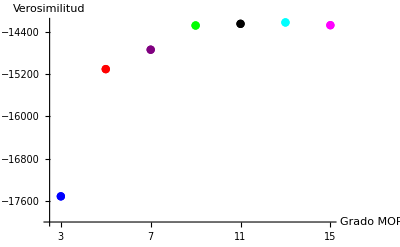

```mathematica
l1 =ListPlot[L,PlotStyle->{{Blue,Thin,PointSize[0.015]},{Red,Thin,PointSize[0.015]},{Purple,Thin,PointSize[0.015]},{Green,Thin,PointSize[0.015]},{Black,Thin,PointSize[0.015]},{Cyan,Thin,PointSize[0.015]},{Magenta,Thin,PointSize[0.015]}},AxesLabel->{"Grado MOP","Verosimilitud"},AxesOrigin->{2.5,-18000},AxesStyle->Directive[Black, 12],PlotRange->Full,Ticks->{{3,5,7,9,11,13,15}, Automatic}]
```

```mathematica
L1={{3,-17514.362189921725},{5,-15106.732615016916},{7,-14739.141461845138},{9,-14281.166384891609},{11,-14249.440595123264},{13,-14223.372977331725},{15,-14275.84437389673}}
```

{{3,-17514.4},{5,-15106.7},{7,-14739.1},{9,-14281.2},{11,-14249.4},{13,-14223.4},{15,-14275.8}}

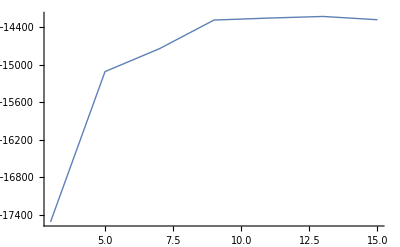

```mathematica
l2= ListLinePlot[L1,PlotStyle->Thin,PlotRange->Full]
```

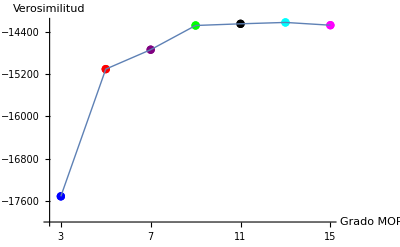

```mathematica
GrafVNMuestra2=Show[l1,l2]
```

```mathematica
(*Comparación verosimilitudes con ambas muestras*)
```

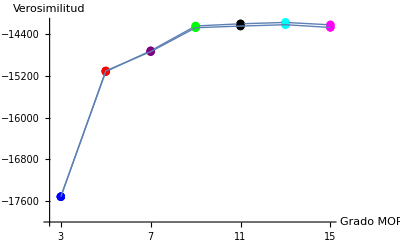

```mathematica
Show[GrafVNMuestra1,GrafVNMuestra2]
```

### MOMENTOS

```mathematica
Muestrales=Table[(Apply[Plus,data^i])/10000,{i,1,16}]
```

{-0.0196627,0.992368,-0.0566338,2.9755,-0.355927,14.7766,-2.60393,100.868,-17.1996,860.688,-67.3493,8625.74,763.198,96986.7,29202.8,1.18282×10^6}

```mathematica
f3estimada = Table[Integrate[x^i*f3[x],{x,-4,4}],{i,1,16}]
```

{-0.0256098,3.25941,-0.0737632,22.7576,0.249636,205.911,11.7594,2133.42,232.362,24040.2,3924.39,286863.,62674.2,3.56849×10^6,976829.,4.58163×10^7}

```mathematica
f5estimada = Table[Integrate[x^i*f5[x],{x,-4,4}],{i,1,16}]
```

{-0.0229081,1.91068,-0.0659814,10.71,-0.414674,99.9965,-5.97032,1209.85,-108.744,16474.4,-1952.38,236564.,-33642.1,3.48413×10^6,-561493.,5.20034×10^7}

```mathematica
f7estimada = Table[Integrate[x^i*f7[x],{x,-4,4}],{i,1,16}]
```

{-0.0189106,1.74006,-0.0544674,10.4039,-0.342312,100.409,-2.50433,1169.68,-7.63143,14770.5,290.414,194408.,9908.22,2.6247×10^6,224552.,3.60739×10^7}

```mathematica
f9estimada = Table[Integrate[x^i*f9[x],{x,-4,4}],{i,1,16}]
```

{-0.0197439,1.19402,-0.0568678,4.8843,-0.357397,36.512,-2.61469,371.009,-17.2707,4395.19,-86.6255,56646.9,-231.589,769062.,-2464.56,1.08123×10^7}

```mathematica
f11estimada = Table[Integrate[x^i*f11[x],{x,-4,4}],{i,1,16}]
```

{-0.0192174,1.13963,-0.0553511,4.53763,-0.347866,33.065,-2.54496,330.337,-16.8101,3875.06,-65.824,49504.3,697.668,664070.,26319.2,9.18104×10^6}

```mathematica
f13estimada = Table[Integrate[x^i*f13[x],{x,-4,4}],{i,1,16}]
```

{-0.0191941,1.08013,-0.0552841,3.97419,-0.347444,26.6485,-2.54187,250.585,-16.7897,2831.58,-65.7442,35380.7,745.01,468528.,29078.9,6.43287×10^6}

```mathematica
f15estimada = Table[Integrate[x^i*f15[x],{x,-4,4}],{i,1,16}]
```

{-0.0187141,1.16883,-0.0539016,4.98556,-0.338755,38.6764,-2.47831,402.292,-16.3698,4828.79,-64.1001,62493.7,726.379,845048.,27793.9,1.17527×10^7}

```mathematica
Table[{Integrate[x^i*f7[x],{x,-4,4}],Integrate[x^i*f9[x],{x,-4,4}],Integrate[x^i*f11[x],{x,-4,4}],Integrate[x^i*f13[x],{x,-4,4}],Integrate[x^i*f15[x],{x,-4,4}]},{i,1,16}]
```

### CRITERIO DE INFORMACIÓN BAYESIANA

```mathematica
B = {{{3,35066.41044183449}},{{5,30298.7306175353}},{{7,29517.397965590433}},{{9,28587.093928271548}},{{11,28522.619116628066}},{{13,28488.547096825852}},{{15,28599.093651794763}}}
```

{{{3,35066.4}},{{5,30298.7}},{{7,29517.4}},{{9,28587.1}},{{11,28522.6}},{{13,28488.5}},{{15,28599.1}}}

```mathematica
B1 = {{3,35066.41044183449},{5,30298.7306175353},{7,29517.397965590433},{9,28587.093928271548},{11,28522.619116628066},{13,28488.547096825852},{15,28599.093651794763}}
```

{{3,35066.4},{5,30298.7},{7,29517.4},{9,28587.1},{11,28522.6},{13,28488.5},{15,28599.1}}

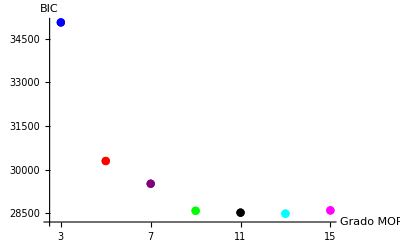

```mathematica
b1 =ListPlot[B,PlotStyle->{{Blue,Thin,PointSize[0.015]},{Red,Thin,PointSize[0.015]},{Purple,Thin,PointSize[0.015]},{Green,Thin,PointSize[0.015]},{Black,Thin,PointSize[0.015]},{Cyan,Thin,PointSize[0.015]},{Magenta,Thin,PointSize[0.015]}},AxesLabel->{"Grado MOP","BIC"},AxesOrigin->{2.5,28200},AxesStyle->Directive[Black, 12],PlotRange->Full,Ticks->{{3,5,7,9,11,13,15}, Automatic}]
```

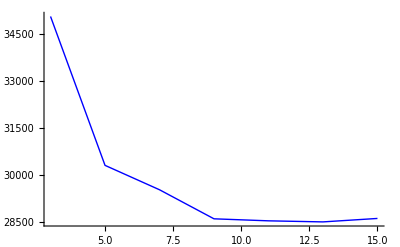

```mathematica
b2= ListLinePlot[B1,PlotStyle->{Blue,Thin},PlotRange->Full]
```

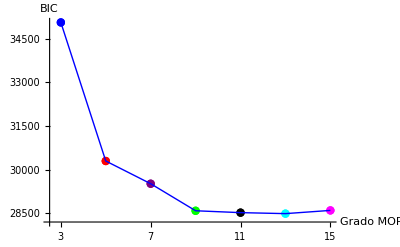

```mathematica
GrafBicNormalMuestra1M = Show[b1,b2]
```

```mathematica
(*Gráfico BIC con otra muestra*)
```

```mathematica
BICN3 =  -2*L3 + 4*Log[10000]
```

35065.6

```mathematica
BICN5=  -2*L5 + 6*Log[10000]
```

30268.7

```mathematica
BICN7 =  -2*L7 + 8*Log[10000]
```

29552.

```mathematica
BICN9 =  -2*L9 + 10*Log[10000]
```

28654.4

```mathematica
BICN11 =  -2*L11 + 12*Log[10000]
```

28609.4

```mathematica
BICN13 =  -2*L13 + 14*Log[10000]
```

28575.7

```mathematica
BICN15 =  -2*L15 + 16*Log[10000]
```

28699.1

```mathematica
BN = {{{3,35065.56574133135}},{{5,30268.72727226569}},{{7,29551.965646666085}},{{9,28654.436173502996}},{{11,28609.405274710243}},{{13,28575.690719871116}},{{15,28699.05419374508}}}
```

{{{3,35065.6}},{{5,30268.7}},{{7,29552.}},{{9,28654.4}},{{11,28609.4}},{{13,28575.7}},{{15,28699.1}}}

```mathematica
BN1 = {{3,35065.56574133135},{5,30268.72727226569},{7,29551.965646666085},{9,28654.436173502996},{11,28609.405274710243},{13,28575.690719871116},{15,28699.05419374508}}
```

{{3,35065.6},{5,30268.7},{7,29552.},{9,28654.4},{11,28609.4},{13,28575.7},{15,28699.1}}

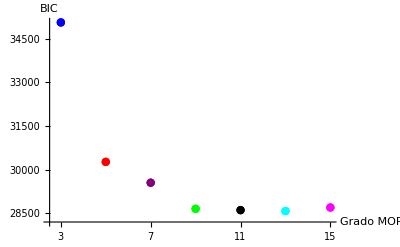

```mathematica
b1N =ListPlot[BN,PlotStyle->{{Blue,Thin,PointSize[0.015]},{Red,Thin,PointSize[0.015]},{Purple,Thin,PointSize[0.015]},{Green,Thin,PointSize[0.015]},{Black,Thin,PointSize[0.015]},{Cyan,Thin,PointSize[0.015]},{Magenta,Thin,PointSize[0.015]}},AxesLabel->{"Grado MOP","BIC"},AxesOrigin->{2.5,28200},AxesStyle->Directive[Black, 12],PlotRange->Full,Ticks->{{3,5,7,9,11,13,15}, Automatic}]
```

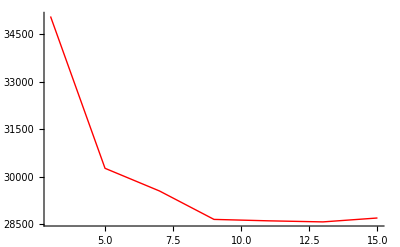

```mathematica
b2N = ListLinePlot[BN1,PlotStyle->{Red,Thin},PlotRange->Full]
```

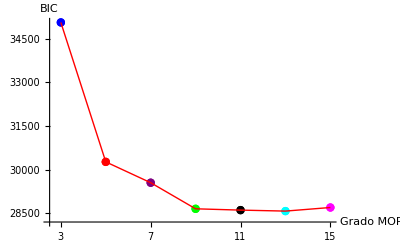

```mathematica
GrafBicNormalMuestra2M =Show[b1N,b2N]
```

```mathematica
(*Comparación verosimilitudes con ambas muestras*)
```

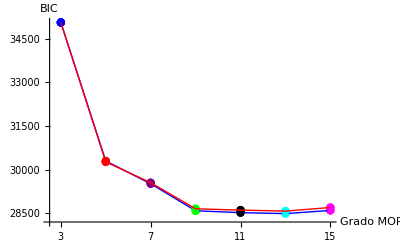

```mathematica
Show[GrafBicNormalMuestra1M,GrafBicNormalMuestra2M]
```